# Classic Monetary Model

## Equilibrium Dynamics under Alternative Monetary Policy Rules

## Equilibrium under an Interest Rate Rule

### Calibration

Time period

```mathematica
Δt=0.25;
```

Discount factor

```mathematica
β=0.99;
```

Relative Risk Aversion

```mathematica
γ=1;
```

Frisch elasticity of labor supply

```mathematica
φ=1;
```

Return to scale

```mathematica
α=1/3;
```

Aggregator coefficient

```mathematica
ϵ=6;
```

Semi-elasticity of money demand

```mathematica
η=4;
```

Measure of price stickiness

```mathematica
θ=2/3;
```

Monetary policy coefficient (1)

```mathematica
ϕπ=1.5;
```

Monetary policy coefficient (2)

```mathematica
ϕy=0.5/4;
```

Other parameters

```mathematica
Θ=(1-α)/(1-α+α*ϵ);
```

```mathematica
λ=((1-θ)*(1-β*θ))/θ*Θ;
```

```mathematica
κ=λ*(γ+(φ+α)/(1-α));
```

### The Effects of a Monetary Policy Shock

AR coefficient of exogenous component of interest rate

```mathematica
ρv=0.5;
```

Other parameters

```mathematica
Λv=1/((1-β*ρv)*(γ*(1-ρv)+ϕy)+κ*(ϕπ-ρv));
```

Monetary policy shock

```mathematica
ϵv[1]=0.0025;
ϵv[t_]:=0;
```

Exogenous component of interest rate

```mathematica
v[0]:=0;
v[t_]:=ρv*v[t-1]+ϵv[t]
```

Output gap

```mathematica
yt[t_]:=-(1-β*ρv)*Λv*v[t]
```

Inflation

```mathematica
Π[t_]:=-κ*Λv*v[t]
```

Nominal interest rate

```mathematica
i[t_]:=(γ*(1-ρv)*(1-β*ρv)-ρv*κ)*Λv*v[t]
```

Real interest rate

```mathematica
r[t_]:=γ*(1-ρv)*(1-β*ρv)*Λv*v[t]
```

Money Growth

```mathematica
dm[t_]:=-Λv*((1-β*ρv)*(1+η*γ*(1-ρv))+κ*(1-η*ρv))*(v[t]-v[t-1])
```

Plots

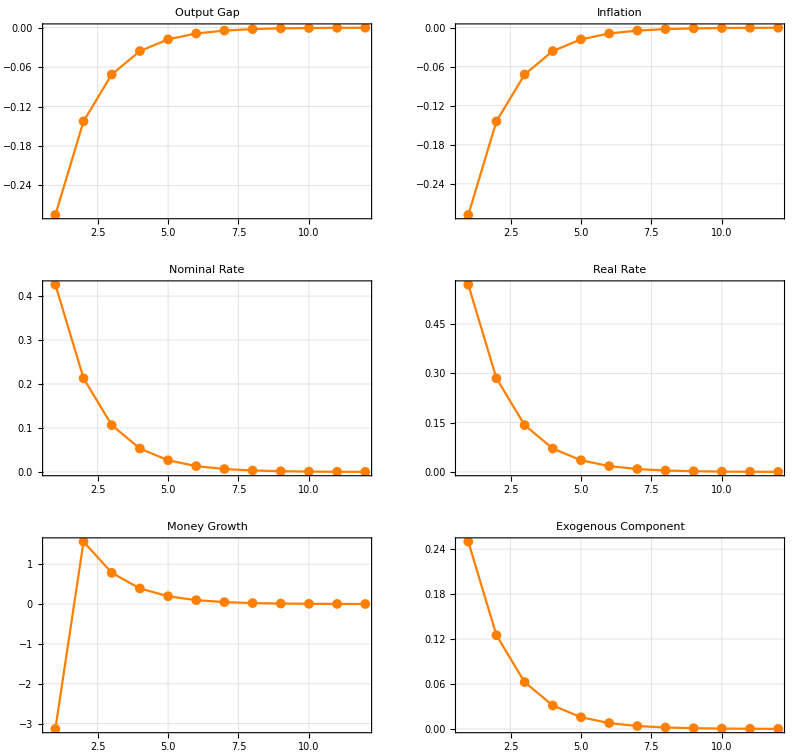

```mathematica
outputgap=ListLinePlot[Table[100*yt[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Output Gap",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
inflation=ListLinePlot[Table[400*Π[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Inflation",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
nominalrate=ListLinePlot[Table[400*i[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Nominal Rate",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
realrate=ListLinePlot[Table[400*r[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Real Rate",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
moneygrowth=ListLinePlot[Table[400*dm[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Money Growth",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
exogcomponent=ListLinePlot[Table[100*v[t],{t,1,12,1}],
PlotMarkers->{Automatic,10},
PlotRange->All, 
PlotLabel->"Exogenous Component",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
GraphicsGrid[{{outputgap,inflation},{nominalrate,realrate},{moneygrowth,exogcomponent}}]
```

### The Effects of a Technology Shock

AR coefficient of technology

```mathematica
ρa=0.9;
```

Other parameters

```mathematica
ψya=(1+φ)/(γ*(1-α)+φ+α);
```

```mathematica
Λa=1/((1-β*ρa)*(γ*(1-ρa)+ϕy)+κ*(ϕπ-ρa));
```

Technology shock

```mathematica
ϵa[1]=0.01;
ϵa[t_]:=0;
```

Technology

```mathematica
a[0]:=0;
a[t_]:=ρa*a[t-1]+ϵa[t]
```

Output gap

```mathematica
yt[t_]:=-γ*ψya*(1-ρa)*(1-β*ρa)*Λa*a[t]
```

Inflation

```mathematica
Π[t_]:=-γ*ψya*(1-ρa)*κ*Λa*a[t]
```

Output

```mathematica
y[t_]:=ψya*(1-γ*(1-ρa)*(1-β*ρa)*Λa)*a[t]
```

Employment

```mathematica
n[t_]:=(ψya-1-γ*ψya*(1-ρa)*(1-β*ρa)*Λa)/(1-α)*a[t]
```

Nominal interest rate

```mathematica
i[t_]:=-γ*ψya*(1-ρa)*(1+κ*Λa*ρa)*a[t]
```

Real interest rate

```mathematica
r[t_]:=-γ*ψya*(1-ρa)*a[t]
```

Money Growth

```mathematica
dm[t_]:=ψya*(1-ρa)*(-γ*κ*Λa-γ*(1-β*ρa)*Λa+η*γ*(1+κ*Λa*ρa))*(a[t]-a[t-1])
```

Plots

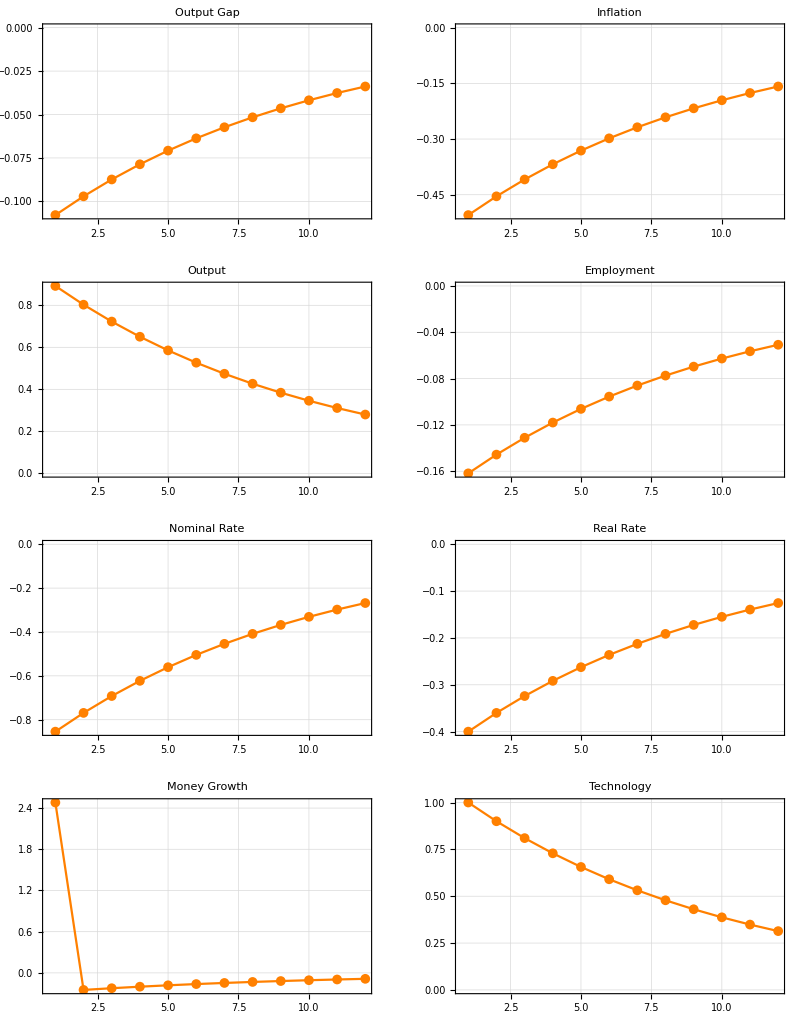

```mathematica
outputgap=ListLinePlot[Table[100*yt[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Output Gap",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
inflation=ListLinePlot[Table[400*Π[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Inflation",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
output=ListLinePlot[Table[100*y[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Output",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
employent=ListLinePlot[Table[100*n[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Employment",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
nominalrate=ListLinePlot[Table[400*i[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Nominal Rate",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
realrate=ListLinePlot[Table[400*r[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Real Rate",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
moneygrowth=ListLinePlot[Table[400*dm[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Money Growth",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
technology=ListLinePlot[Table[100*a[t],{t,1,12,1}],
PlotMarkers->{Automatic, 10},
PlotRange->All, 
PlotLabel->"Technology",
PlotTheme->"Detailed",
PlotStyle->{Orange},
Frame->{{True,True},{True,True}}];
GraphicsGrid[{{outputgap,inflation},{output,employent},{nominalrate,realrate},{moneygrowth,technology}}]
```